```mathematica
create[f_] := 1/Sqrt[2 hbar m w] (-hbar D[f, x] + m w x f)
```

```mathematica
phi0:= (m w/(Pi hbar))^(1/4) Exp[-m w/(2 hbar) x^2]
```

```mathematica
hbar = m = w = 1
```

1

```mathematica
phin[n_]:= 1/Sqrt[n!] Nest[create,phi0,n]
```

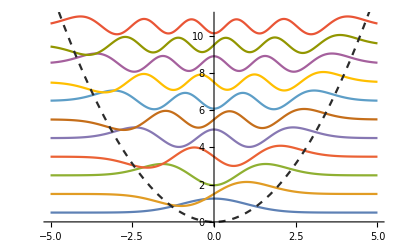

```mathematica
Show[Plot[Evaluate[Table[phin[n]+(n + 1/2) hbar w,{n,0,10,1}]],{x,-5,5}],Plot[1/2 m w^2 x^2,{x,-5,5} ,PlotStyle->Dashed,ColorFunction->GrayLevel]]
```